```mathematica
Quit[]
```

## Problem 1

## Part a

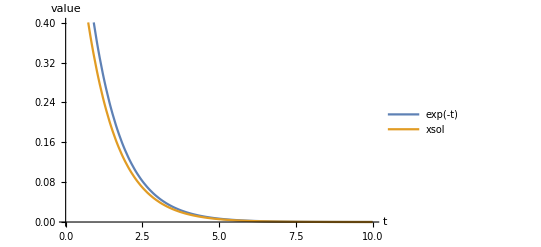

```mathematica
ClearAll["Global`*"]
sol =NDSolve[{x'[t]== -Sin[x[t]], x[0]==.8}, x, {t, 0, 10}];
xsol = x[t]/.sol[[1]];
Plot[{Exp[-t],xsol},{t,0,10}, AxesLabel->{t, value},PlotLegends->"Expressions"]
```

## Part b

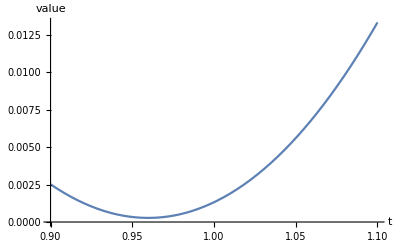

```mathematica
J[x0_]:= Integrate[(Exp[-t]-(x[t]/.NDSolve[{x'[t]== -Sin[x[t]], x[0]==x0}, x, {t, 0, 10}]))^2, {t, 0, 10}];
Plot[J[x0], {x0, .9, 1.1}, AxesLabel->{t, value}]
(*J looks like it minimizes at about 0.96*)
```

## Part c & d

```mathematica
ClearAll["Global`*"]
L = (Exp[-t]-x[t])^2;
DL = D[L, x[t]];
(*make z0 something random just so mathematica can symbolically integrate - I'll divide through by this later*)
z0 = 3;
xsol[x0_]:=NDSolve[{x'[t]== -Sin[x[t]], x[0]==x0}, x, {t, 0, 10}][[1]]
zsol[x0_]:= NDSolve[{z'[t]==(-Sin[x[t]]/x[t]/.xsol[x0])*z[t], z[0] == z0}, z, {t, 0, 10}][[1]]

DJ[x0_]:= NIntegrate[(DL/.xsol[x0])*z[t]/.zsol[x0], {t, 0, 10}]/z0

x0 = 1;
ϵ= .000001;
grad =DJ[x0];
While[Abs[grad]>ϵ,
x0 = x0-grad;
grad= DJ[x0];
Print[x0];
]
```

0.953495

0.961947

0.960494

0.960747

0.960703

0.960711

0.960709

## Problem 2

## Part a

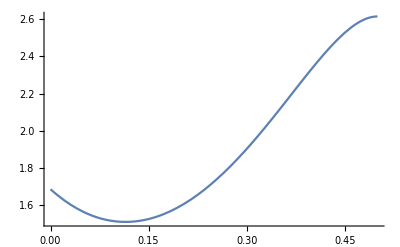

```mathematica
ClearAll["Global`*"]
x[t] = {x1[t], x2[t]};
dx[t] = D[x[t], t];
a1 = {{-1, 0}, {1, 2}};
a2 = {{1, 1}, {1, -2}};
x0 = {1,1};

sol1=NDSolve[Flatten[{Thread[dx[t]==a1.x[t]], {x1[0], x2[0]}==x0}], {x1, x2}, {t, 0,0.5}];
sol2[τ_]:=NDSolve[Flatten[{Thread[dx[t]==a2.x[t]], x1[τ]==(x1[τ]/.sol1[[1]]),  x2[τ]==(x2[τ]/.sol1[[1]])}], {x1, x2}, {t, τ,0.5}]

J[τ_]:=NIntegrate[(x[t].x[t]/.sol1[[1]]), {t, 0, τ}]+NIntegrate[(x[t].x[t]/.sol2[τ][[1]]), {t, τ, .5}]

Plot[J[τ], {τ, 0, .5}]
```

## Parts b & c

```mathematica
Dl = 2*x[t];
z[t]={z1[t], z2[t]};
dz[t]=D[z[t], t];

zsol[τ_]:= NDSolve[Flatten[{Thread[dz[t]==a2.z[t]], Thread[z[t] == a1.x[t]-a2.x[t]/.sol1[[1]]/.t->τ]}], {z1, z2}, {t, τ, .5}]

(*use newly simulated z and simulated x from part a*)
dJdτ[τ_]:= NIntegrate[(Dl/.sol2[τ][[1]]).z[t]/.zsol[τ][[1]], {t, τ, .5}]

dJdτ[.25]
```

3.06982

## Part d

```mathematica
τ = .25;
ϵ= .00001;
der = dJdτ[τ];
While[Abs[der]>ϵ,
τ = τ-.05*der;
der = dJdτ[τ];
Print[τ];
]
```

0.0965089

0.119686

0.113433

0.115028

0.114615

0.114722

0.114694

0.114701

0.114699